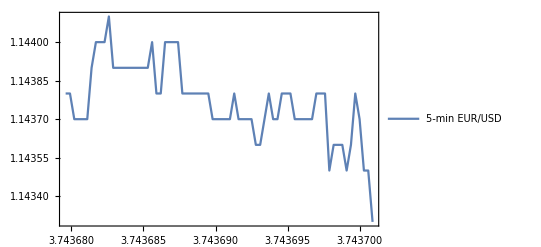

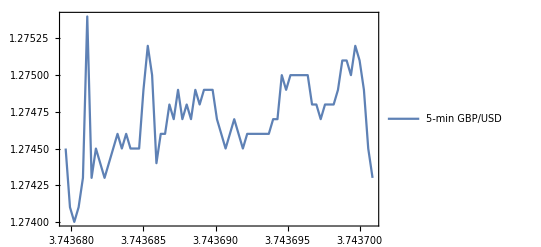

```mathematica
EURUSD=Import["/Users/wanghaibiao/Desktop/5-min.xlsx",{"Data",1,Table[i,{i,2,73}],{1,3}}];
eurusd=Import["/Users/wanghaibiao/Desktop/5-min.xlsx",{"Data",1,Table[i,{i,2,73}],3}];
GBPUSD=Import["/Users/wanghaibiao/Desktop/5-min.xlsx",{"Data",1,Table[i,{i,2,73}],{1,2}}];
gbpusd=Import["/Users/wanghaibiao/Desktop/5-min.xlsx",{"Data",1,Table[i,{i,2,73}],2}];
date=Import["/Users/wanghaibiao/Desktop/5-min.xlsx",{"Data",1,Table[i,{i,2,73}],1}];
DateListPlot[EURUSD,PlotLegends->Placed[{"5-min EUR/USD"},Above]]
DateListPlot[GBPUSD,PlotLegends->Placed[{"5-min GBP/USD"},Above]]
```

5-min we change different size of observation, we can not obtain a successful size of observation to estimate the model. For 1-hour, half-hour, 15-min, we all choose 3-day data, they are all successful.

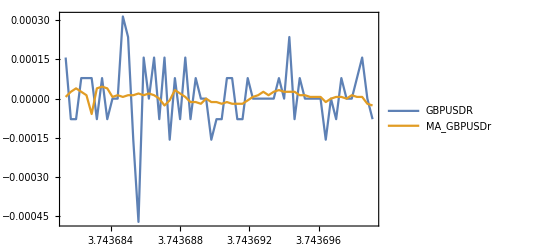

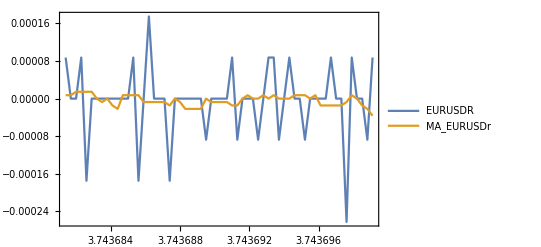

```mathematica
gbpusdr=Differences[Log[gbpusd]];
eurusdr=Differences[Log[eurusd]];
GBPUSDr=Table[{date[[i+6]],gbpusdr[[i+6]]},{i,1,60}];EURUSDr=Table[{date[[i+6]],eurusdr[[i+6]]},{i,1,60}];
mMAgbpusdr=MovingAverage[gbpusdr,12];
mMAeurusdr=MovingAverage[eurusdr,12];
mMAGBPUSDr=Table[{date[[i+6]],mMAgbpusdr[[i]]},{i,1,60}];mMAEURUSDr=Table[{date[[i+6]],mMAeurusdr[[i]]},{i,1,60}];
DateListPlot[{GBPUSDr,mMAGBPUSDr},PlotRange->{All,All},PlotLegends->Placed[{"GBPUSDR","MA_GBPUSDr"},Above]]
DateListPlot[{EURUSDr,mMAEURUSDr},PlotRange->{All,All},PlotLegends->Placed[{"EURUSDR","MA_EURUSDr"},Above]]
```

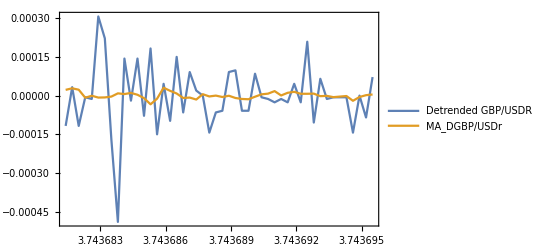

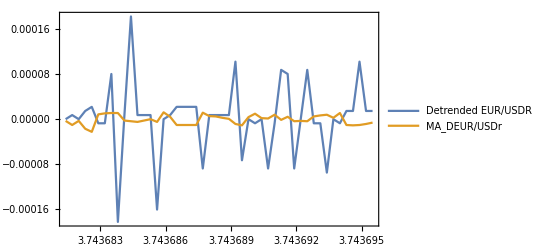

```mathematica
Dgbpusdr= Take[Drop[gbpusdr,6],60]-mMAgbpusdr;
Deurusdr= Take[Drop[eurusdr,6],60]-mMAeurusdr;
DGBPUSDr=Table[{date[[i+6]],Dgbpusdr[[i+6]]},{i,1,48}];
DEURUSDr=Table[{date[[i+6]],Deurusdr[[i+6]]},{i,1,48}];
mMADgbpusdr=MovingAverage[Dgbpusdr,12];
mMADeurusdr=MovingAverage[Deurusdr,12];
mMADGBPUSDr=Table[{date[[i+6]],mMADgbpusdr[[i]]},{i,1,48}];mMADEURUSDr=Table[{date[[i+6]],mMADeurusdr[[i]]},{i,1,48}];
DateListPlot[{DGBPUSDr,mMADGBPUSDr},PlotRange->{All,All},PlotLegends->Placed[{"Detrended GBP/USDR","MA_DGBP/USDr"},Above]]
DateListPlot[{DEURUSDr,mMADEURUSDr},PlotRange->All,PlotLegends->Placed[{"Detrended EUR/USDR","MA_DEUR/USDr"},Above]]
```

```mathematica
NSolve[m+theta==Mean[Dgbpusdr*100]&&sigma^2+theta^2==Variance[Dgbpusdr*100]&&(2*theta^3+3sigma^2*theta)/(sigma^2+theta^2)^1.5==Skewness[Dgbpusdr*100]&&sigma>0,{m,theta,sigma},Reals]
NSolve[m+theta==Mean[Deurusdr*100]&&sigma^2+theta^2==Variance[Deurusdr*100]&&(2*theta^3+3sigma^2*theta)/(sigma^2+theta^2)^1.5==Skewness[Deurusdr*100]&&sigma>0,{m,theta,sigma},Reals]
```

{{theta→-0.00286623,sigma→0.0116894,m→0.0031604}}

{{theta→-0.00247292,sigma→0.00696056,m→0.0024365}}

```mathematica
Subscript[θ, 1]=-0.002866232357769179;
Subscript[m, 1]=0.00316039743072588;
Subscript[σ, 1]=0.011689443358235645;
Subscript[θ, 2]=-0.002472918718227994;
Subscript[m, 2]=0.0024364984067488022;
Subscript[σ, 2]=0.0069605587128325165;
```

```mathematica
F=Function[x,((2*Exp[Subscript[θ, 1]*(x-Subscript[m, 1])/Subscript[σ, 1]^2])/(Subscript[σ, 1]*Sqrt[2*Pi]*Gamma[1]))*((x-Subscript[m, 1])^2/(2*Subscript[σ, 1]^2+Subscript[θ, 1]^2))^0.25*BesselK[0.5,Sqrt[(x-Subscript[m, 1])^2*(2*Subscript[σ, 1]^2+Subscript[θ, 1]^2)]/Subscript[σ, 1]^2]][x]
```

59.6018 ⅇ^(-20.9761 (-0.0031604+x)-122.787 √((-0.0031604+x)^2)) (1+0./(√((-0.0031604+x)^2)))

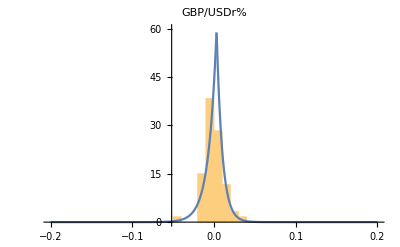

```mathematica
Show[Histogram[Dgbpusdr*100,Automatic,"ProbabilityDensity"],Plot[F,{x,-0.2,0.2},PlotRange->{Full,Full}],PlotRange->{All,{0,60}},PlotLabel->"GBP/USDr%"]
```

```mathematica
G=Function[x,((2*Exp[(Subscript[θ, 2])*(x-Subscript[m, 2])/Subscript[σ, 2]^2])/(Subscript[σ, 2]*Sqrt[2*Pi]*Gamma[1]))*((x-Subscript[m, 2])^2/(2*Subscript[σ, 2]^2+Subscript[θ, 2]^2))^0.25*BesselK[0.5,Sqrt[(x-Subscript[m, 2])^2*(2*Subscript[σ, 2]^2+Subscript[θ, 2]^2)]/Subscript[σ, 2]^2]][x]
```

98.5262 ⅇ^(-51.0413 (-0.0024365+x)-209.488 √((-0.0024365+x)^2)) (1+0./(√((-0.0024365+x)^2)))

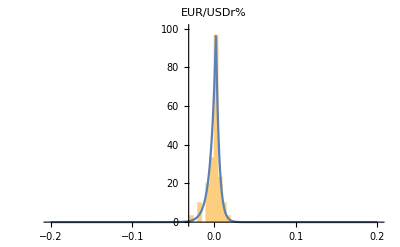

```mathematica
Show[Histogram[Deurusdr*100,Automatic,"ProbabilityDensity"],Plot[G,{x,-0.2,0.2},PlotRange->{Full,Full}],PlotRange->{All,{0,100}},PlotLabel->"EUR/USDr%"]
```

```mathematica
𝒟1=ProbabilityDistribution[F,{x,-Infinity,Infinity}];
DistributionFitTest[Dgbpusdr*100,𝒟1,"PearsonChiSquare"]
𝒟2=ProbabilityDistribution[G,{x,-Infinity,Infinity}];
DistributionFitTest[Deurusdr*100,𝒟2,"PearsonChiSquare"]
```

0.00120043

1.51235×10^-10

```mathematica
R12=Sin[Pi*KendallTau[Dgbpusdr*100,Deurusdr*100]/2];
R={{1,R12},{R12,1}};
MatrixForm[R]
```

```mathematica
L1=Dgbpusdr*100;
L2=Deurusdr*100;
```

```mathematica
data=Table[{L1[[i]],L2[[i]]},{i,1,60}];
```

```mathematica
EstimatedDistribution[data,CopulaDistribution[{"MultivariateT",R,v},{StudentTDistribution[v],StudentTDistribution[v]}],ParameterEstimator->"MaximumLikelihood"]
```

```mathematica
ν=;
```

```mathematica
A=CholeskyDecomposition[R];
dist=ProductDistribution[NormalDistribution[],NormalDistribution[],ChiSquareDistribution[ν]];
z1=RandomVariate[MarginalDistribution[dist,1],60];
z2=RandomVariate[MarginalDistribution[dist,2],60];
s=RandomVariate[MarginalDistribution[dist,3],60];
For[i=1,i≤60,i++,
Subscript[s, i]=s[[i]];
Subscript[y, i]=A.{z1[[i]],z2[[i]]};
Subscript[x, i]=Sqrt[ν]/Sqrt[Subscript[s, i]]*Subscript[y, i]];
x1=Table[Subscript[x, i][[1]],{i,60}];
x2=Table[Subscript[x, i][[2]],{i,60}];
Subscript[u, 1]=CDF[StudentTDistribution[ν],x1];
Subscript[u, 2]=CDF[StudentTDistribution[ν],x2];
```

```mathematica
Subscript[Sim1, 0]=Take[Drop[gbpusd,5],1][[1]];
Subscript[Sim2, 0]=Take[Drop[eurusd,5],1][[1]];
dates=Take[Drop[date,6],60];
S1=Take[Drop[gbpusd,6],60];
S2=Take[Drop[eurusd,6],60];
Subscript[L, 1]=InverseCDF[𝒟1,Subscript[u, 1]];
Subscript[L, 2]=InverseCDF[𝒟2,Subscript[u, 2]];
For[t=1,t≤60,t++,
Subscript[L, 1,t]=Subscript[L, 1][[t]];
Subscript[L, 2,t]=Subscript[L, 2][[t]];
Subscript[Sim1, t]=Subscript[Sim1, t-1]*Exp[mMAgbpusdr[[t]]+Subscript[L, 1,t]/100];
Subscript[Sim2, t]=Subscript[Sim2, t-1]*Exp[mMAeurusdr[[t]]+Subscript[L, 2,t]/100]];
Sm1=Table[{dates[[t]],Subscript[Sim1, t]},{t,1,60}];
Sm2=Table[{dates[[t]],Subscript[Sim2, t]},{t,1,60}];
DateListPlot[{Sm1,Table[{dates[[t]],S1[[t]]},{t,1,60}]},PlotLegends->Placed[{"sim GBPUSD","GBPUSD"},Above]]
DateListPlot[{Sm2,Table[{dates[[t]],S2[[t]]},{t,1,60}]},PlotLegends->Placed[{"sim EURUSD","EURUSD"},Above]]
```